```mathematica
SubPlus[𝒩][α_]= 1/√(4 e^(-α^2)Cosh[α^2]);
SubMinus[𝒩][α_]= 1/√(4 e^(-α^2)Sinh[α^2]);


(* From Nomrlaizations.nb we have *)
SubPlus[ℳ][α_]=1/(2 √2 √(ⅇ^(-α^2) (Cosh[α^2]+Cos[α^2])));
SubMinus[ℳ][α_]=1/(2 √2 √(ⅇ^(-α^2) (Cosh[α^2]-Cos[α^2])));


Subscript[ℳ, +ℰ][α_]=1/(2 √2 √(ⅇ^(-α^2) (Sinh[α^2]-Sin[α^2])));
Subscript[ℳ, -ℰ][α_]=1/(2 √2 √(ⅇ^(-α^2) (Sinh[α^2]+Sin[α^2])));
```

for even

```mathematica
Simplify[Expand[ⅇ^(-α^2/2(1-γ))((SubPlus[ℳ][α])/(SubPlus[ℳ][√γ α]))],{1>γ>0,α>0}]
FullSimplify[Expand[ⅇ^(-α^2/2(1-γ))((SubMinus[ℳ][α])/(SubMinus[ℳ][√γ α]))],{1>γ>0,α>0}]
```

1/(√((Cos[α^2]+Cosh[α^2])/(Cos[α^2 γ]+Cosh[α^2 γ])))

-(√((-Cos[α^2]+Cosh[α^2]) (-Cos[α^2 γ]+Cosh[α^2 γ])))/(Cos[α^2]-Cosh[α^2])

```mathematica
Simplify[Expand[ⅇ^(-α^2/2(1-γ))((SubPlus[ℳ][α])/(SubMinus[ℳ][√γ α]))],{1>γ>0,α>0}]
FullSimplify[Expand[ⅇ^(-α^2/2(1-γ))((SubMinus[ℳ][α])/(SubPlus[ℳ][√γ α]))],{1>γ>0,α>0}]
```

1/(√((Cos[α^2]+Cosh[α^2])/(-Cos[α^2 γ]+Cosh[α^2 γ])))

1/(√((-Cos[α^2]+Cosh[α^2])/(Cos[α^2 γ]+Cosh[α^2 γ])))

for odd

```mathematica
FullSimplify[Expand[ⅇ^(-α^2/2(1-γ))((SubPlus[ℳ][α])/(Subscript[ℳ, +ℰ][√γ α]))],{1>γ>0,α>0}]
FullSimplify[Expand[ⅇ^(-α^2/2(1-γ))((SubMinus[ℳ][α])/(Subscript[ℳ, -ℰ][√γ α]))],{1>γ>0,α>0}]
```

√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))

√((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))

```mathematica
FullSimplify[Expand[ⅇ^(-α^2/2(1-γ))((SubPlus[ℳ][α])/(Subscript[ℳ, -ℰ][√γ α]))],{1>γ>0,α>0}]
FullSimplify[Expand[ⅇ^(-α^2/2(1-γ))((SubMinus[ℳ][α])/(Subscript[ℳ, +ℰ][√γ α]))],{1>γ>0,α>0}]
```

√((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))

-(√((Cos[α^2]-Cosh[α^2]) (Sin[α^2 γ]-Sinh[α^2 γ])))/(Cos[α^2]-Cosh[α^2])

```mathematica
f[n_]=( √(1-γ)α)^n/(√2 √(n!));
```

```mathematica
ip[s1_,s2_,α_]=ⅇ^(-α^2)ⅇ^(s1*s2 α^2);
slist= {1,-1,ⅈ,-ⅈ};

cflist[μ_,ℰ_] := {1,(-1)^ℰ,ⅈ^ℰ(-1)^μ,ⅈ^ℰ(-1)^(ℰ+μ)};

ℳ[μ_,ℰ_,α_]:=1/√FullSimplify[(∑_(i=1)^4 ∑_(j=1)^4 cflist[μ,ℰ][[i]]*cflist[μ,ℰ][[j]]ip[slist[[i]],slist[[j]],α]),α>0];
```

```mathematica
(* k =4n *)
mat[4n,0]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]+Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];
mat[4n,1]=0;
mat[4n,2]=0;
mat[4n,3]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]-Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];

(* k = 4n+2 *)
mat[4n+2,0]=0;
mat[4n+2,1]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]+Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];
mat[4n+2,2]=ⅈ Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]-ⅈ Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];
mat[4n+2,3]=0;
```

```mathematica
{mat[4n,#]&/@ Range[0,3,1],mat[4n+2,#]&/@ Range[0,3,1]}//MatrixForm
```

(√((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) | 0 | 0 | -√((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))
0 | √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) | -ⅈ √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+ⅈ √(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) | 0)

```mathematica
(* k = 4n+1 *)
mat[4n+1,0]=ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]+ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];


mat[4n+1,1]=ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]-ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];


mat[4n+1,2]=-ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]+ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];


mat[4n+1,3]=ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]-ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];
{mat[4n+1,#]&/@ Range[0,3,1]}//MatrixForm
```

((ⅇ^((ⅈ π)/4) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2)+(ⅇ^(-(ⅈ π)/4) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2) | (ⅇ^((ⅈ π)/4) √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2)-(ⅇ^(-(ⅈ π)/4) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2) | -(ⅇ^(-(ⅈ π)/4) √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2)+(ⅇ^((ⅈ π)/4) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2) | (ⅇ^((ⅈ π)/4) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2)-(ⅇ^(-(ⅈ π)/4) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2))

```mathematica
(* k = 4n+3 *)
mat[4n+3,0]=ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]+ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];


mat[4n+3,1]=ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]-ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];


mat[4n+3,2]=ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]-ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];


mat[4n+3,3]=ⅇ^(-ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]-ⅇ^(ⅈ π/4)/(√2)Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];
{mat[4n+3,#]&/@ Range[0,3,1]}//MatrixForm
```

((ⅇ^(-(ⅈ π)/4) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2)+(ⅇ^((ⅈ π)/4) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2) | (ⅇ^(-(ⅈ π)/4) √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2)-(ⅇ^((ⅈ π)/4) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2) | (ⅇ^((ⅈ π)/4) √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2)-(ⅇ^(-(ⅈ π)/4) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2) | (ⅇ^(-(ⅈ π)/4) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(√2)-(ⅇ^((ⅈ π)/4) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))/(√2))

```mathematica
Zeros = ConstantArray[0,4];
w[n_]=
{
(f[4n]mat[4n,#]&/@ Range[0,3,1])~Join~Zeros,
(f[4n+2]mat[4n+2,#]&/@ Range[0,3,1])~Join~Zeros,
Zeros~Join~(f[4n+1]mat[4n+1,#]&/@ Range[0,3,1]),
Zeros~Join~(f[4n+3]mat[4n+3,#]&/@ Range[0,3,1])
};
```

```mathematica
W[n_,α_,γ_]=Simplify[w[n]ᵀ.w[n]*,{α>0,1>γ>0,n>=0,Sinh[α^2]>Sin[α^2],Cosh[α^2]>Cos[α^2],Sinh[α^2 γ]>Sin[α^2 γ],Cosh[α^2 γ]>Cos[α^2 γ],Sinh[α^2]+Sin[α^2]>0,Cosh[α^2]+Cos[α^2]>0,Sinh[α^2 γ]+Sin[α^2 γ]>0,Cosh[α^2 γ]+Cos[α^2 γ]>0}];
```

```mathematica
W[n,α,γ]//MatrixForm
```

((α^(8 n) (1-γ)^(4 n) (√((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))^2)/(2 (4 n)!) | 0 | 0 | (α^(8 n) (1-γ)^(4 n) (-Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/((Cos[α^2]^2-Cosh[α^2]^2) (4 n)!) | 0 | 0 | 0 | 0
0 | (α^(4+8 n) (1-γ)^(2+4 n) (√((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))^2)/(2 (2+4 n)!) | (ⅈ α^(4+8 n) (1-γ)^(2+4 n) (√((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-√(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))))/(2 (2+4 n)!) | 0 | 0 | 0 | 0 | 0
0 | (ⅈ α^(4+8 n) (1-γ)^(2+4 n) (-√((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))))/(2 (2+4 n)!) | (α^(4+8 n) (1-γ)^(2+4 n) (√((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-√(-(Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))^2)/(2 (2+4 n)!) | 0 | 0 | 0 | 0 | 0
(α^(8 n) (1-γ)^(4 n) (-Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/((Cos[α^2]^2-Cosh[α^2]^2) (4 n)!) | 0 | 0 | (α^(8 n) (1-γ)^(4 n) (√((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))^2)/(2 (4 n)!) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (α^(2+8 n) (1-γ)^(1+4 n) (α^4 (-1+γ)^2 (1+4 n)!+(3+4 n)!) (-ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))))/(4 (1+4 n)! (3+4 n)!) | 1/4 α^(2+8 n) (1-γ)^(1+4 n) (((√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((1+4 n)!)+(α^4 (-1+γ)^2 (√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((3+4 n)!)) | -(α^(2+8 n) (1-γ)^(1+4 n) (ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/(4 (1+4 n)!)-(α^(6+8 n) (1-γ)^(3+4 n) (√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (ⅈ √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/(4 (3+4 n)!) | 1/2 α^(1+4 n) (1-γ)^(1/2+2 n) (((α √(1-γ))^(1+4 n) (√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))^2)/(2 (1+4 n)!)+(α^(5+4 n) (1-γ)^(5/2+2 n) (√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))^2)/(2 (3+4 n)!))
0 | 0 | 0 | 0 | -(α^(2+8 n) (1-γ)^(1+4 n) (-ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (-ⅈ √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/(4 (1+4 n)!)-(α^(6+8 n) (1-γ)^(3+4 n) (ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (ⅈ √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/(4 (3+4 n)!) | (α^(2+8 n) (1-γ)^(1+4 n) (α^4 (-1+γ)^2 (1+4 n)!+(3+4 n)!) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/(4 (1+4 n)! (3+4 n)!) | -1/4 ⅈ α^(2+8 n) (1-γ)^(1+4 n) ((α^4 (-1+γ)^2 (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))^2)/((3+4 n)!)+((√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))^2)/((1+4 n)!)) | 1/4 α^(2+8 n) (1-γ)^(1+4 n) (((√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((1+4 n)!)+(α^4 (-1+γ)^2 (-ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (ⅈ √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((3+4 n)!))
0 | 0 | 0 | 0 | 1/4 α^(2+8 n) (1-γ)^(1+4 n) ((α^4 (-1+γ)^2 (ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((3+4 n)!)+((√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (ⅈ √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((1+4 n)!)) | 1/4 ⅈ α^(2+8 n) (1-γ)^(1+4 n) (((√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))^2)/((1+4 n)!)+(α^4 (-1+γ)^2 (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))^2)/((3+4 n)!)) | (α^(2+8 n) (1-γ)^(1+4 n) (α^4 (-1+γ)^2 (1+4 n)!+(3+4 n)!) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/(4 (1+4 n)! (3+4 n)!) | 1/4 α^(2+8 n) (1-γ)^(1+4 n) (((ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((1+4 n)!)-(α^4 (-1+γ)^2 (-ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((3+4 n)!))
0 | 0 | 0 | 0 | 1/2 α^(1+4 n) (1-γ)^(1/2+2 n) ((α^(5+4 n) (1-γ)^(5/2+2 n) (√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))^2)/(2 (3+4 n)!)+((α √(1-γ))^(1+4 n) (√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])))^2)/(2 (1+4 n)!)) | 1/4 α^(2+8 n) (1-γ)^(1+4 n) (((√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+ⅈ √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((1+4 n)!)+(α^4 (-1+γ)^2 (ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (-ⅈ √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((3+4 n)!)) | 1/4 α^(2+8 n) (1-γ)^(1+4 n) (-(α^4 (-1+γ)^2 (ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((3+4 n)!)+((-ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+ⅈ √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))/((1+4 n)!)) | (α^(2+8 n) (1-γ)^(1+4 n) (α^4 (-1+γ)^2 (1+4 n)!+(3+4 n)!) (-ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))) (ⅈ √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))))/(4 (1+4 n)! (3+4 n)!))

```mathematica
Subscript[η, eff] = T/(1-η (1-T));
W[n,√T(* this √T is for the noiseless attenuatiuon due to ideal ZPS *)α/(√Subscript[η, eff]),Subscript[η, eff] γ]//MatrixForm
```

((((√T α)/(√(T/(1-(1-T) η))))^(8 n) (1-(T γ)/(1-(1-T) η))^(4 n) (√((Cos[T α^2 γ]-Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/(2 (4 n)!) | 0 | 0 | (((√T α)/(√(T/(1-(1-T) η))))^(8 n) (1-(T γ)/(1-(1-T) η))^(4 n) (Cos[α^2 (1-(1-T) η)] Cosh[T α^2 γ]-Cos[T α^2 γ] Cosh[α^2 (1-(1-T) η)]))/((Cos[α^2 (1-(1-T) η)]^2-Cosh[α^2 (1-(1-T) η)]^2) (4 n)!) | 0 | 0 | 0 | 0
0 | (((√T α)/(√(T/(1-(1-T) η))))^(4+8 n) (1-(T γ)/(1-(1-T) η))^(2+4 n) (√(-(Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((-Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/(2 (2+4 n)!) | (ⅈ ((√T α)/(√(T/(1-(1-T) η))))^(4+8 n) (1-(T γ)/(1-(1-T) η))^(2+4 n) (-√(-(Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((-Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))) (√(-(Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((-Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(2 (2+4 n)!) | 0 | 0 | 0 | 0 | 0
0 | (ⅈ ((√T α)/(√(T/(1-(1-T) η))))^(4+8 n) (1-(T γ)/(1-(1-T) η))^(2+4 n) (√(-(Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-√((-Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))) (√(-(Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((-Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(2 (2+4 n)!) | (((√T α)/(√(T/(1-(1-T) η))))^(4+8 n) (1-(T γ)/(1-(1-T) η))^(2+4 n) (-√(-(Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((-Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/(2 (2+4 n)!) | 0 | 0 | 0 | 0 | 0
(((√T α)/(√(T/(1-(1-T) η))))^(8 n) (1-(T γ)/(1-(1-T) η))^(4 n) (Cos[α^2 (1-(1-T) η)] Cosh[T α^2 γ]-Cos[T α^2 γ] Cosh[α^2 (1-(1-T) η)]))/((Cos[α^2 (1-(1-T) η)]^2-Cosh[α^2 (1-(1-T) η)]^2) (4 n)!) | 0 | 0 | (((√T α)/(√(T/(1-(1-T) η))))^(8 n) (1-(T γ)/(1-(1-T) η))^(4 n) (√((Cos[T α^2 γ]-Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-√((Cos[T α^2 γ]+Cosh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/(2 (4 n)!) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (1+4 n)!+(3+4 n)!) (-ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))))/(4 (1+4 n)! (3+4 n)!) | 1/4 ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (((√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))-ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((1+4 n)!)+(α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((3+4 n)!)) | -(((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(4 (1+4 n)!)-(((√T α)/(√(T/(1-(1-T) η))))^(6+8 n) (1-(T γ)/(1-(1-T) η))^(3+4 n) (√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (ⅈ √((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(4 (3+4 n)!) | 1/2 ((√T α)/(√(T/(1-(1-T) η))))^(1+4 n) (1-(T γ)/(1-(1-T) η))^(1/2+2 n) ((((√T α √(1-(T γ)/(1-(1-T) η)))/(√(T/(1-(1-T) η))))^(1+4 n) (√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))-ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)])))^2)/(2 (1+4 n)!)+(((√T α)/(√(T/(1-(1-T) η))))^(5+4 n) (1-(T γ)/(1-(1-T) η))^(5/2+2 n) (√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)])))^2)/(2 (3+4 n)!))
0 | 0 | 0 | 0 | -(((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (-ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (-ⅈ √((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(4 (1+4 n)!)-(((√T α)/(√(T/(1-(1-T) η))))^(6+8 n) (1-(T γ)/(1-(1-T) η))^(3+4 n) (ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (ⅈ √((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(4 (3+4 n)!) | (((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (1+4 n)!+(3+4 n)!) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(4 (1+4 n)! (3+4 n)!) | -1/4 ⅈ ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) ((α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/((3+4 n)!)+((√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/((1+4 n)!)) | 1/4 ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (((√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))-ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((1+4 n)!)+(α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (-ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (ⅈ √((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((3+4 n)!))
0 | 0 | 0 | 0 | 1/4 ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) ((α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((3+4 n)!)+((√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (ⅈ √((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((1+4 n)!)) | 1/4 ⅈ ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (((√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/((1+4 n)!)+(α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)])))^2)/((3+4 n)!)) | (((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (1+4 n)!+(3+4 n)!) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/(4 (1+4 n)! (3+4 n)!) | 1/4 ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (((ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((1+4 n)!)-(α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (-ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((3+4 n)!))
0 | 0 | 0 | 0 | 1/2 ((√T α)/(√(T/(1-(1-T) η))))^(1+4 n) (1-(T γ)/(1-(1-T) η))^(1/2+2 n) ((((√T α)/(√(T/(1-(1-T) η))))^(5+4 n) (1-(T γ)/(1-(1-T) η))^(5/2+2 n) (√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))-ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)])))^2)/(2 (3+4 n)!)+(((√T α √(1-(T γ)/(1-(1-T) η)))/(√(T/(1-(1-T) η))))^(1+4 n) (√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)])))^2)/(2 (1+4 n)!)) | 1/4 ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (((√((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+ⅈ √(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((1+4 n)!)+(α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (-ⅈ √((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+√((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((3+4 n)!)) | 1/4 ((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (-(α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))-ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((3+4 n)!)+((-ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (√((Sin[T α^2 γ]-Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))+ⅈ √((Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))))/((1+4 n)!)) | (((√T α)/(√(T/(1-(1-T) η))))^(2+8 n) (1-(T γ)/(1-(1-T) η))^(1+4 n) (α^4 (1-(1-T) η)^2 (-1+(T γ)/(1-(1-T) η))^2 (1+4 n)!+(3+4 n)!) (-ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))) (ⅈ √((-Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]+Cosh[α^2 (1-(1-T) η)]))+√(-(Sin[T α^2 γ]+Sinh[T α^2 γ])/(Cos[α^2 (1-(1-T) η)]-Cosh[α^2 (1-(1-T) η)]))))/(4 (1+4 n)! (3+4 n)!))

```mathematica
Simplify[∑_(n=0)^∞ W[n,α,γ]]
```

```mathematica
𝒲[α_,γ_]=1/2{{1/(Cos[α^2]^2-Cosh[α^2]^2)(Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cosh[α^2] Cosh[α^2 γ]-Cosh[α^2]^2 √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Cos[α^2 γ]+Cos[α^2] √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),0,0,((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2),0,0,0,0},{0,-1/(Cos[α^2]^2-Cosh[α^2]^2)(Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (-Cos[α^2] Cos[α^2 γ]-Cosh[α^2] Cosh[α^2 γ]+Cos[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))),-(ⅈ (Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2),0,0,0,0,0},{0,(ⅈ (Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2),1/(Cos[α^2]^2-Cosh[α^2]^2)(Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2] Cos[α^2 γ]+Cosh[α^2] Cosh[α^2 γ]+Cos[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))),0,0,0,0,0},{((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2),0,0,1/(Cos[α^2]^2-Cosh[α^2]^2)(Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cosh[α^2] Cosh[α^2 γ]+Cosh[α^2]^2 √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Cos[α^2 γ]-Cos[α^2] √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),0,0,0,0},{0,0,0,0,(Sinh[α^2 (-1+γ)] (Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2),1/2 (ⅈ Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+Sinh[α^2 (-1+γ)] (-√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),1/2 (Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),-1/(Cos[α^2]^2-Cosh[α^2]^2)(Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]+Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]-ⅈ Cos[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))+ⅈ Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2])))},{0,0,0,0,1/2 (-ⅈ Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+Sinh[α^2 (-1+γ)] (-√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),(Sinh[α^2 (-1+γ)] (-Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2),(4 ⅈ Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]-4 ⅈ Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]+2 Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+(-1-2 Cos[2 α^2]+Cosh[2 α^2]) Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(2 (Cos[2 α^2]-Cosh[2 α^2])),1/2 ⅈ (Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))},{0,0,0,0,1/2 (Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))-ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),(-4 ⅈ Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]+4 ⅈ Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]+2 Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+(-1-2 Cos[2 α^2]+Cosh[2 α^2]) Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(2 (Cos[2 α^2]-Cosh[2 α^2])),(Sinh[α^2 (-1+γ)] (-Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2),1/2 (-Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))-ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))},{0,0,0,0,-1/(Cos[α^2]^2-Cosh[α^2]^2)(Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]+Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]+ⅈ Cos[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-ⅈ Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))),1/2 (-ⅈ Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))-Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),1/2 (-Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),(Sinh[α^2 (-1+γ)] (Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(Cos[α^2]^2-Cosh[α^2]^2)}};
```

```mathematica
𝒲[α,γ]//MatrixForm
```

(((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cosh[α^2] Cosh[α^2 γ]-Cosh[α^2]^2 √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Cos[α^2 γ]+Cos[α^2] √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 0 | 0 | ((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 0 | 0 | 0 | 0
0 | -((Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (-Cos[α^2] Cos[α^2 γ]-Cosh[α^2] Cosh[α^2 γ]+Cos[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | -(ⅈ (Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 0 | 0 | 0 | 0 | 0
0 | (ⅈ (Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | ((Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2] Cos[α^2 γ]+Cosh[α^2] Cosh[α^2 γ]+Cos[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 0 | 0 | 0 | 0 | 0
((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 0 | 0 | ((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cosh[α^2] Cosh[α^2 γ]+Cosh[α^2]^2 √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Cos[α^2 γ]-Cos[α^2] √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (Sinh[α^2 (-1+γ)] (Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 1/4 (ⅈ Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+Sinh[α^2 (-1+γ)] (-√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))) | 1/4 (Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))) | -(Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]+Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]-ⅈ Cos[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))+ⅈ Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2])))/(2 (Cos[α^2]^2-Cosh[α^2]^2))
0 | 0 | 0 | 0 | 1/4 (-ⅈ Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+Sinh[α^2 (-1+γ)] (-√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))) | (Sinh[α^2 (-1+γ)] (-Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | (4 ⅈ Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]-4 ⅈ Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]+2 Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+(-1-2 Cos[2 α^2]+Cosh[2 α^2]) Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(4 (Cos[2 α^2]-Cosh[2 α^2])) | 1/4 ⅈ (Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))
0 | 0 | 0 | 0 | 1/4 (Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))-ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))) | (-4 ⅈ Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]+4 ⅈ Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]+2 Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+(-1-2 Cos[2 α^2]+Cosh[2 α^2]) Sin[α^2 (-1+γ)] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))/(4 (Cos[2 α^2]-Cosh[2 α^2])) | (Sinh[α^2 (-1+γ)] (-Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 1/4 (-Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))-ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))))
0 | 0 | 0 | 0 | -(Cosh[α^2] Sin[α^2 γ] Sinh[α^2 (-1+γ)]+Cos[α^2] Sinh[α^2 (-1+γ)] Sinh[α^2 γ]+ⅈ Cos[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-ⅈ Cosh[α^2]^2 Sin[α^2 (-1+γ)] √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2])))/(2 (Cos[α^2]^2-Cosh[α^2]^2)) | 1/4 (-ⅈ Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))-√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))-Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))) | 1/4 (-Sin[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2]))+√((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))+ⅈ Sinh[α^2 (-1+γ)] (√((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))-√(-(Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))) | (Sinh[α^2 (-1+γ)] (Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]))/(2 (Cos[α^2]^2-Cosh[α^2]^2)))

```mathematica
𝒲[2,0.5]//MatrixForm
```

(0.459151 | 0 | 0 | -0.0199895 | 0 | 0 | 0 | 0
0 | 0.574884 | 0.+0.038748 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.038748 ⅈ | 0.00261167 | 0 | 0 | 0 | 0 | 0
-0.0199895 | 0 | 0 | 0.000870263 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.239537 | -0.0604001-0.0584878 ⅈ | 0.00139995-0.240914 ⅈ | -0.0546493-0.058471 ⅈ
0 | 0 | 0 | 0 | -0.0604001+0.0584878 ⅈ | 0.242429 | 0.058471+0.0661855 ⅈ | 0.240914+0.00139995 ⅈ
0 | 0 | 0 | 0 | 0.00139995+0.240914 ⅈ | 0.058471-0.0661855 ⅈ | 0.242429 | 0.0584878-0.0604001 ⅈ
0 | 0 | 0 | 0 | -0.0546493+0.058471 ⅈ | 0.240914-0.00139995 ⅈ | 0.0584878+0.0604001 ⅈ | 0.239537)

### Purely Mathematica

```mathematica
A[i_,j_]:=ArrayFlatten[Base[i]†.Base[j]];
Ar = Table[A[i,j],{i,1,8},{j,1,8}];
Dimensions[Arᵀ]
```

{8,8,4,4}

```mathematica
ClearAll[X];
Χ=Table[X[i,j],{i,1,8},{j,1,8}];
Χ//MatrixForm
```

(X[1,1] | X[1,2] | X[1,3] | X[1,4] | X[1,5] | X[1,6] | X[1,7] | X[1,8]
X[2,1] | X[2,2] | X[2,3] | X[2,4] | X[2,5] | X[2,6] | X[2,7] | X[2,8]
X[3,1] | X[3,2] | X[3,3] | X[3,4] | X[3,5] | X[3,6] | X[3,7] | X[3,8]
X[4,1] | X[4,2] | X[4,3] | X[4,4] | X[4,5] | X[4,6] | X[4,7] | X[4,8]
X[5,1] | X[5,2] | X[5,3] | X[5,4] | X[5,5] | X[5,6] | X[5,7] | X[5,8]
X[6,1] | X[6,2] | X[6,3] | X[6,4] | X[6,5] | X[6,6] | X[6,7] | X[6,8]
X[7,1] | X[7,2] | X[7,3] | X[7,4] | X[7,5] | X[7,6] | X[7,7] | X[7,8]
X[8,1] | X[8,2] | X[8,3] | X[8,4] | X[8,5] | X[8,6] | X[8,7] | X[8,8])

```mathematica
ClearAll[a];
𝒲=Module[{a},
1/2 ((a=Table[RandomComplex[],{4},{4}])+ConjugateTranspose[a])
];

Χ={{x11,x12,x13,x14},{x21,x22,x23,x24},{x31,x32,x33,x34},{x41,x42,x43,x44}};
Ar = Table[1/2 PauliMatrix[i]PauliMatrix[j],{i,0,3},{j,0,3}];
Ar//MatrixForm
```

((1/2 | 0
0 | 1/2) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (1/2 | 0
0 | -1/2)
(0 | 0
0 | 0) | (0 | 1/2
1/2 | 0) | (0 | -ⅈ/2
ⅈ/2 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | -ⅈ/2
ⅈ/2 | 0) | (0 | -1/2
-1/2 | 0) | (0 | 0
0 | 0)
(1/2 | 0
0 | -1/2) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (1/2 | 0
0 | 1/2))

```mathematica
SemidefiniteOptimization[
 -1/4 Tr[N[𝒲] . Χ], 
{∑_(i=0)^3 ∑_(j=0)^3 Χ[[i+1,j+1]]Ar[i,j]== IdentityMatrix[4], Χ (\[VectorGreaterEqual])_4 0},
ArrayFlatten[Χ,1],Method->"CSDP"]
```

```mathematica
(* Creating a matrix of free parameters (8×8) *)
Χ=Table[X[i,j],{i,1,8},{j,1,8}];

(* Creating a random Hermitian matrix (8×8) *)
𝒲=Module[{a},
1/2 ((a=Table[RandomComplex[],{8},{8}])+ConjugateTranspose[a])
]; 

(* Creating basis matrices (2×4) matrices *)
Base[l_]:=1/(√2)ArrayFlatten[{{UnitStep[-(l-4-1/2)]PauliMatrix[Mod[l-1,4]],UnitStep[l-4-1/2]PauliMatrix[Mod[l-1,4]]}}];

(* SDP *)
SemidefiniteOptimization[-1/4 Tr[𝒲 . Χ], {∑_(i=1)^8 ∑_(j=1)^8 (X[i,j]Base[i]†.Base[j])== IdentityMatrix[4], Χ (\[VectorGreaterEqual])_8 0},ArrayFlatten[Χ,1]]
```

SemidefiniteOptimization::herm: The matrix … is not Hermitian or real and symmetric.

```mathematica
tmp =∑_(i=1)^8 ∑_(j=1)^8 X[i,j]Base[i]†.Base[j];
```

```mathematica
Solve[{tmp==IdentityMatrix[4]},ArrayFlatten[Χ,1]]
```

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[Χ,1] must be at least equal to the specified rank 1. (The rank is given by the optional second argument, which defaults to 2.)

{}

```mathematica
(* Creating a matrix of free parameters (8×8) *)
Χ=Table[X[i,j],{i,1,8},{j,1,8}];


(* Creating a random Hermitian matrix (8×8) *)
𝒲=Module[{a},
1/2 ((a=Table[RandomComplex[],{8},{8}])+ConjugateTranspose[a])
]; 

(* Creating basis matrices (2×4) matrices *)
Base[l_]:=1/(√2)ArrayFlatten[{{UnitStep[-(l-4-1/2)]PauliMatrix[Mod[l-1,4]],UnitStep[l-4-1/2]PauliMatrix[Mod[l-1,4]]}}];

(* SDP *)
SemidefiniteOptimization[-1/4 Tr[𝒲. Χ], {∑_(i=1)^8 ∑_(j=1)^8 (X[i,j]Base[i]†.Base[j])== IdentityMatrix[4], Χ (\[VectorGreaterEqual])_8 0},ArrayFlatten[Χ,1]]
```

SemidefiniteOptimization::herm: The matrix … is not Hermitian or real and symmetric.

### MATLink

```mathematica
Needs["MatLink`"]
Quiet[OpenMATLAB[]]
<<ToMatlab`
```

MScript::shdw: Symbol MScript appears in multiple contexts {MATLink`,Global`}; definitions in context MATLink` may shadow or be shadowed by other definitions.

Needs::nocont: Context MatLink` was not created when Needs was evaluated.

```mathematica
(* Base*)
MScript["base","
function B = base(l)
	B = [(1/sqrt(2))*paulimatrix(mod(l-1,4))* heaviside((9/2)-l), (1/sqrt(2))* paulimatrix(mod(l-1,4))* heaviside(l-(9/2))];
end
","Overwrite" -> True ];


(* PauliMatrix*)
MScript["paulimatrix","
function p = paulimatrix(k)
	if ( k == 1 )
        p = [0 1;1 0];
    elseif ( k == 2 )
        p = [0 -1i;1i 0];
    elseif ( k == 3 )
        p = [1 0;0 -1];
    else
        p = eye(2);
    end
end
","Overwrite" -> True ];



(* test_𝒲 *)
MScript["scW","
function process = scW(d)
	a = (complex(rand(d, d), rand(d, d)));
	process = (1/2)*(a' + a);
end
","Overwrite" -> True ];
```

```mathematica
(* Export 𝒲 process matrix from Mathematica to MATALB via MATLink *)
MSet["Wmat",𝒲[2,.5]];
```

```mathematica
export𝒲[2,0.5]
```

(0.459151+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0199895+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.574884+0. ⅈ | 0.+0.038748 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.-0.038748 ⅈ | 0.00261167+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.0199895+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.000870263+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.239537+0. ⅈ | -0.0604001-0.0584878 ⅈ | 0.00139995-0.240914 ⅈ | -0.0546493-0.058471 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0604001+0.0584878 ⅈ | 0.242429+0. ⅈ | 0.058471+0.0661855 ⅈ | 0.240914+0.00139995 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.00139995+0.240914 ⅈ | 0.058471-0.0661855 ⅈ | 0.242429+0. ⅈ | 0.0584878-0.0604001 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0546493+0.058471 ⅈ | 0.240914-0.00139995 ⅈ | 0.0584878+0.0604001 ⅈ | 0.239537+0. ⅈ)

```mathematica
scriptSDP=MScript["sdp",
"

d= 2;
d2 = 4; % d^2
dE = 8; % Number of error spaces * d^2

numErrorSpaces = 2;

cvx_begin sdp

	variable X(dE,dE) hermitian semidefinite
	expression sum(d2,d2) 
	dual variable Y
	
	% Objective function
	maximise ((1/d2)* trace(Wmat.'* X)) % Note that paranthesis should evelpe the whole expression

	subject to
	
	
	sum = 0*eye(d2);
	for i = 1:dE
		for j = 1:dE
             sum = sum + X(i,j)*( base(i)'* base(j) ); 
		end
	end

	% Equality Constraint
	Y: eye(d2) == sum;

cvx_end","Overwrite" -> True ];
```

```mathematica
ExeSDP[α_,γ_]:=
Module[{},
MSet["Wmat",𝒲[α,γ]];
MEvaluate[scriptSDP]
];
```

```mathematica
ExeSDP[2,1]
```

Calling SDPT3 4.0: 64 variables, 18 equality constraints
------------------------------------------------------------

 num. of constraints = 18
 dim. of sdp    var  = 16,   num. of sdp  blk  =  1
 number of nearly dependent constraints = 8
 To remove these constraints, re-run sqlp.m with OPTIONS.rmdepconstr = 1.
*******************************************************************
   SDPT3: Infeasible path-following algorithms
*******************************************************************
 version  predcorr  gam  expon  scale_data
   HKM      1      0.000   1        0    
it pstep dstep pinfeas dinfeas  gap      prim-obj      dual-obj    cputime
-------------------------------------------------------------------
 0|0.000|0.000|2.1e+01|3.0e+01|2.6e+03|-8.000000e+00  0.000000e+00| 0:0:00| chol  1  1 
 1|1.000|1.000|7.6e-06|1.0e-01|7.5e+01|-2.612530e-01 -7.506425e+01| 0:0:00| chol  1  1 
 2|1.000|0.968|8.4e-08|1.3e-02|2.4e+00|-2.717323e-01 -2.624215e+00| 0:0:00| chol  1  1 
 3|1.000|1.000|1.1e-08|1.0e-03|1.1e+00|-8.616526e-01 -1.925809e+00| 0:0:00| chol  1  1 
 4|1.000|0.958|7.7e-09|1.4e-04|4.4e-02|-9.885788e-01 -1.032009e+00| 0:0:00| chol  1  1 
 5|0.988|0.988|2.5e-09|1.2e-05|5.4e-04|-9.998601e-01 -1.000366e+00| 0:0:00| chol  1  1 
 6|0.989|0.989|7.9e-10|1.1e-06|5.9e-06|-9.999985e-01 -1.000001e+00| 0:0:00| chol  1  1 
 7|1.000|0.997|4.4e-11|3.9e-09|8.0e-08|-1.000000e+00 -1.000000e+00| 0:0:00| chol  1  1 
 8|1.000|0.998|9.1e-13|1.7e-11|9.7e-10|-1.000000e+00 -1.000000e+00| 0:0:00|
  stop: max(relative gap, infeasibilities) < 1.49e-08
-------------------------------------------------------------------
 number of iterations   =  8
 primal objective value = -1.00000000e+00
 dual   objective value = -1.00000000e+00
 gap := trace(XZ)       = 9.69e-10
 relative gap           = 3.23e-10
 actual relative gap    = 3.07e-10
 rel. primal infeas (scaled problem)   = 9.15e-13
 rel. dual     "        "       "      = 1.75e-11
 rel. primal infeas (unscaled problem) = 0.00e+00
 rel. dual     "        "       "      = 0.00e+00
 norm(X), norm(y), norm(Z) = 3.2e+00, 7.1e-01, 6.1e-01
 norm(A), norm(b), norm(C) = 4.3e+00, 3.0e+00, 1.4e+00
 Total CPU time (secs)  = 0.05  
 CPU time per iteration = 0.01  
 termination code       =  0
 DIMACS: 1.4e-12  0.0e+00  1.9e-11  0.0e+00  3.1e-10  3.2e-10
-------------------------------------------------------------------
 
------------------------------------------------------------
Status: Solved
Optimal value (cvx_optval): +1

```mathematica
ℱ[α_,γ_]:=
Module[{},
MSet["Wmat",𝒲[α,γ]];
MEvaluate[scriptSDP];
MEvaluate["Fidelity = cvx_optval;"];
MGet["Fidelity"]
];

ℱzps[α_,γ_,η_,T_]  := Module[{ηnew,αnew},
ηnew=(T η)/(1-(1-T)η);
αnew= α/(√ηnew);
ℱ[√T αnew,ηnew  γ]
];
```

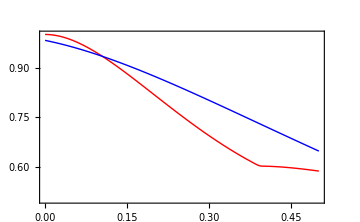

```mathematica
Module[{α,η, T,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
α=2;
η=0.95;
T=0.50;
losslimit = 0.5;

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

xlabel =Text[Style["1-γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],{losslimit+0.04,(1-losslimit)+0.005},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["ℱ_ℰ"
,{FontSize->axesLabelSize,FontFamily->fam,Black}],{.0,1+losslimit.12},{0,0}];
ylab = Graphics[{ylabel}];

plt = Plot[{ℱ [α,1-l],ℱzps [α,1-l,η,T]},{l, 0,losslimit},PlotRange->{1-losslimit,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None];

Show[{plt,xlab,ylab}]
]
```

```mathematica
Module[{α,η, T,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam },
α=2;
T=0.50;
losslimit = 0.5;

titleSize = 24;
axesLabelSize = 20;
fam = "CMU Sans Serif";

Δℱ[l_,η_]:=ℱzps [α,1-l,η,T]-ℱ [α,1-l];

plt = Plot[{Δℱ[l,1],Δℱ[l,0.75],Δℱ[l,0.5],Δℱ[l,0.25],Δℱ[l,0]},{l, 0,losslimit},PlotRange->Full,LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->All,PlotRangeClipping->False,ImagePadding->{{40, 40}, {40, 50}},PlotRangePadding->None,AxesLabel->{Style["1-γ",{FontSize->axesLabelSize,FontFamily->fam,Black}],Style["Δℱ_ℰ"
,{FontSize->axesLabelSize,FontFamily->fam,Black}]},
ColorFunction-> Function[{l,y},If[y<0,Red,Blue]],
ColorFunctionScaling->False,PlotStyle->Thick];

Show[{plt}]
]
```